```mathematica
ClearAll["`*"]
$PreRead=(#/.
s_String/;StringMatchQ[s,NumberString]&&Precision@ToExpression@s==MachinePrecision:>s<>"`30."&);
```

```mathematica
order = 3;
kmin = 0.1; R = 10; Z=2; c = 137.036; k =-1;
nnode = 12;
knot = Flatten[{
Table[0, {i, 1,order+1}],
Table[ kmin(R/kmin)^((i-1)/(nnode-2*4)), {i,1, nnode-2*4}],
Table[R, {i, 1,order+1}]}]
n = Length[knot]-order-2
ϕi[r_, i_] := BSplineBasis[{order,knot},i, r]
v=-Z/r;
```

{0,0,0,0,0.1,0.31622776601683793319988935444,1.,3.1622776601683793319988935444,10,10,10,10}

7

```mathematica
Cmat =  Evaluate[Table[Integrate[ϕi[r,ai] ϕi[r,aj],{r,0,R}], {ai,2,n-2}, {aj,2,n-2}]];
{Cmat // Dimensions, SymmetricMatrixQ[Cmat]}
Cmat // MatrixForm // ScientificForm
```

{{4,4},True}

(1.25643370494749897461152323485×10^-1 | 8.7478266774188700540626551681×10^-2 | 7.3271040391968421209143381959×10^-3 | 4.30427178473939576917833410189×10^-5
8.7478266774188700540626551681×10^-2 | 4.04285363867520350935206072748×10^-1 | 2.71837132324057272309026894282×10^-1 | 2.35848354001520974052392337962×10^-2
7.3271040391968421209143381959×10^-3 | 2.71837132324057272309026894282×10^-1 | 1.26086579931238454556103791548 | 6.9118377205087718441952846178×10^-1
4.30427178473939576917833410189×10^-5 | 2.35848354001520974052392337962×10^-2 | 6.9118377205087718441952846178×10^-1 | 9.1561862812472490941020549125×10^-1)

```mathematica
Dmat =  Evaluate[Table[Integrate[ϕi[r,ai] D[ϕi[r,aj], r],{r,0,R}], {ai,2,n-2}, {aj,2,n-2}]];
{Dmat // Dimensions, SymmetricMatrixQ[Dmat]}
Dmat // MatrixForm // ScientificForm
```

{{4,4},False}

(0 | 3.87610275946070056813816742715×10^-1 | 5.17008784050112743026198625291×10^-2 | 4.40642380543309997596526953238×10^-4
-3.87610275946070056813816742715×10^-1 | -1.02823202999947133027898804317×10^-31 | 3.93663179573039737554455657575×10^-1 | 5.22504619921216736613350390617×10^-2
-5.17008784050112743026198625291×10^-2 | -3.93663179573039737554455657575×10^-1 | 1.16457393826477678918871371269×10^-31 | 2.78240388128825152617666758104×10^-1
-4.40642380543309997596526953238×10^-4 | -5.22504619921216736613350390617×10^-2 | -2.78240388128825152617666758104×10^-1 | -1.04122171872446604215118519664×10^-32)

```mathematica
Vmat = Evaluate[Table[Integrate[ϕi[r,ai] v ϕi[r,aj], {r,0,R}], {ai,2,n-2}, {aj,2,n-2}]];
{Vmat // Dimensions, SymmetricMatrixQ[Vmat]}
N[Vmat, 18] // MatrixForm // ScientificForm
```

{{4,4},True}

(-1.29319281097562386 | -5.37151421107165621×10^-1 | -3.06714216894702706×10^-2 | -1.35051719018590103×10^-4
-5.37151421107165621×10^-1 | -1.25430260185981156 | -5.10106409667461082×10^-1 | -3.13240025468201523×10^-2
-3.06714216894702706×10^-2 | -5.10106409667461082×10^-1 | -1.22078633718594952 | -4.37464155645455345×10^-1
-1.35051719018590103×10^-4 | -3.13240025468201523×10^-2 | -4.37464155645455345×10^-1 | -4.23184333801483728×10^-1)

```mathematica
Kmat = Evaluate[Table[Integrate[ϕi[r,ai] k/r ϕi[r,aj],{r,0,R}], {ai,2,n-2}, {aj,2,n-2}]];
{Kmat // Dimensions, SymmetricMatrixQ[Kmat]}
Kmat // MatrixForm
```

{{4,4},True}

(-0.64659640548781192763945521303 | -0.26857571055358281058406214472 | -0.01533571084473513527888305525 | -0.000067525859509295051463170271254
-0.26857571055358281058406214472 | -0.62715130092990577978212876804 | -0.25505320483373054110667906968 | -0.015662001273410076136668318016
-0.01533571084473513527888305525 | -0.25505320483373054110667906968 | -0.610393168592974758145237771 | -0.21873207782272767241913325283
-0.000067525859509295051463170271254 | -0.015662001273410076136668318016 | -0.21873207782272767241913325283 | -0.21159216690074186376622602265)

```mathematica
Aprime = Table[If[k > 0, 
2 c^2 KroneckerDelta[i,1]KroneckerDelta[j,1]- c/2 KroneckerDelta[i,1]KroneckerDelta[j,n-2]- c/2 KroneckerDelta[i,n-2]KroneckerDelta[j,1]+ c/2 KroneckerDelta[i,n-3]KroneckerDelta[j,n-3]- c/2 KroneckerDelta[i,2(n-3)]KroneckerDelta[i,2(n-3)],
c KroneckerDelta[i,1]KroneckerDelta[j,1]- c/2 KroneckerDelta[i,1]KroneckerDelta[j,n-2]- c/2 KroneckerDelta[i,n-2]KroneckerDelta[j,1]+ c/2 KroneckerDelta[i,n-3]KroneckerDelta[j,n-3]- c/2 KroneckerDelta[i,2(n-3)]KroneckerDelta[j,2(n-3)]
],{i,1,2(n-3)},{j,1,2(n-3)}];
{Aprime // Dimensions, SymmetricMatrixQ[Aprime]}
Aprime // MatrixForm
```

{{8,8},True}

(137.036 | 0 | 0 | 0 | -68.518 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 68.518 | 0 | 0 | 0 | 0
-68.518 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -68.518)

```mathematica
Amat = ArrayFlatten[{{Vmat, c (Dmat-Kmat)}, {-c(Dmat+Kmat), Vmat-2c^2 Cmat}}] + Aprime;
{Amat // Dimensions, SymmetricMatrixQ[Amat]}
N[Amat, 20] //MatrixForm //ScientificForm
```

{{8,8},True}

(1.3574280718902437614×10^2 | -5.3715142110716562117×10^-1 | -3.0671421689470270558×10^-2 | -1.3505171901859010293×10^-4 | 2.0088985022427795316×10^1 | 8.9921102845966430337×10^1 | 9.1864260444282489834 | 6.9637342943848785503×10^-2
-5.3715142110716562117×10^-1 | -1.2543026018598115596 | -5.1010640966746108221×10^-1 | -3.1324002546820152273×10^-2 | -1.6312020703124882274×10^1 | 8.5942305674230568438×10^1 | 8.8897498453566171907×10^1 | 9.3064523160554088653
-3.0671421689470270558×10^-2 | -5.1010640966746108221×10^-1 | -1.2207863371859495163 | -4.3746415564545534484×10^-1 | -4.9833371017900009873 | -1.8994556498375975044×10^1 | 8.3645838251306888957×10^1 | 6.8103118844136992932×10^1
-1.3505171901859010293×10^-4 | -3.1324002546820152273×10^-2 | -4.3746415564545534484×10^-1 | 6.8094815666198516272×10^1 | -5.1130395576417272158×10^-2 | -5.0139363030493624784 | -8.1547808111063742965 | 2.8995744183410062043×10^1
2.0088985022427795316×10^1 | -1.6312020703124882274×10^1 | -4.9833371017900009873 | -5.1130395576417272158×10^-2 | -4.7201730525236340231×10^3 | -3.2860223275811912799×10^3 | -2.7522007094539947471×10^2 | -1.6167218525789110224
8.9921102845966430337×10^1 | 8.5942305674230568438×10^1 | -1.8994556498375975044×10^1 | -5.0139363030493624784 | -3.2860223275811912799×10^3 | -1.5185295081026880331×10^4 | -1.0210095887138465335×10^4 | -8.8582421801812381032×10^2
9.1864260444282489834 | 8.8897498453566171907×10^1 | 8.3645838251306888957×10^1 | -8.1547808111063742965 | -2.7522007094539947471×10^2 | -1.0210095887138465335×10^4 | -4.7356478789578463561×10^4 | -2.5959731364404830065×10^4
6.9637342943848785503×10^-2 | 9.3064523160554088653 | 6.8103118844136992932×10^1 | 2.8995744183410062043×10^1 | -1.6167218525789110224 | -8.8582421801812381032×10^2 | -2.5959731364404830065×10^4 | -3.4457498944458853805×10^4)

```mathematica
Bmat = ArrayFlatten[{{Cmat,0}, {0,Cmat}}];
{Bmat // Dimensions, SymmetricMatrixQ[Bmat]}
N[Bmat, 20] //MatrixForm //ScientificForm
```

{{8,8},True}

(1.2564337049474989746×10^-1 | 8.7478266774188700541×10^-2 | 7.3271040391968421209×10^-3 | 4.3042717847393957692×10^-5 | 0 | 0 | 0 | 0
8.7478266774188700541×10^-2 | 4.0428536386752035094×10^-1 | 2.7183713232405727231×10^-1 | 2.3584835400152097405×10^-2 | 0 | 0 | 0 | 0
7.3271040391968421209×10^-3 | 2.7183713232405727231×10^-1 | 1.2608657993123845456 | 6.9118377205087718442×10^-1 | 0 | 0 | 0 | 0
4.3042717847393957692×10^-5 | 2.3584835400152097405×10^-2 | 6.9118377205087718442×10^-1 | 9.1561862812472490941×10^-1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1.2564337049474989746×10^-1 | 8.7478266774188700541×10^-2 | 7.3271040391968421209×10^-3 | 4.3042717847393957692×10^-5
0 | 0 | 0 | 0 | 8.7478266774188700541×10^-2 | 4.0428536386752035094×10^-1 | 2.7183713232405727231×10^-1 | 2.3584835400152097405×10^-2
0 | 0 | 0 | 0 | 7.3271040391968421209×10^-3 | 2.7183713232405727231×10^-1 | 1.2608657993123845456 | 6.9118377205087718442×10^-1
0 | 0 | 0 | 0 | 4.3042717847393957692×10^-5 | 2.3584835400152097405×10^-2 | 6.9118377205087718442×10^-1 | 9.1561862812472490941×10^-1)

```mathematica
energy = Sort[Eigenvalues[N[{Amat, Bmat},30]]] // ScientificForm
```

{-3.7700424914591554695555939154×10^4,-3.7569538852198425914578211576×10^4,-3.7565677169931379948791346834×10^4,-3.7559069950827969434182919632×10^4,-1.3076538796036411038152098171,-1.8346164411646771853452627816×10^-1,1.3913838358215763102747930038×10^2,1.3292110043134898683701506295×10^3}

```mathematica
Plot[energy/(2 c^2),{x,.2,1},PlotStyle->{{Thin, Black}},Axes->{False,True},AspectRatio->2,PlotRange->{{0,1},Automatic}, AxesLabel->E/(2 c.b2)]
```

-Graphics-

#### Plot Fortran result

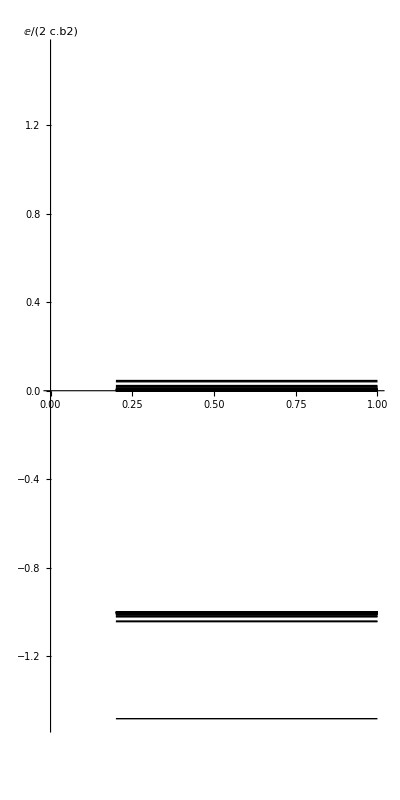

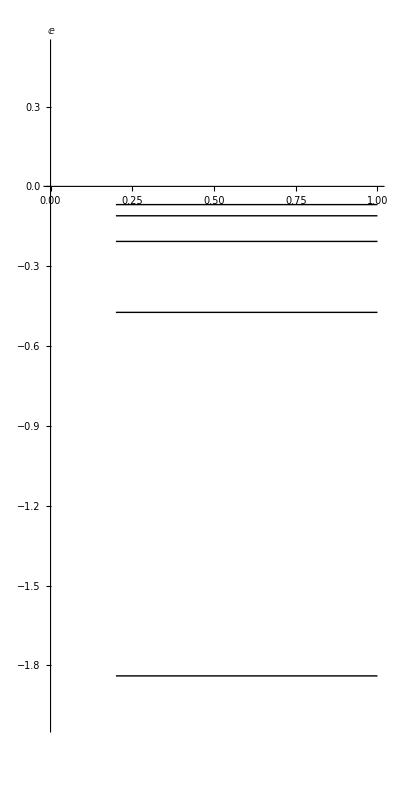

```mathematica
feigval =Import["/home/mathispanet/Documents/Dirac_Equation/eigenvalues.dat", "CSV"];
Plot[feigval/(2 c^2),{x,.2,1},PlotStyle->{{Thin, Black}},Axes->{False,True},AspectRatio->2,PlotRange->{{0,1},Automatic}, AxesLabel->E/(2 c.b2)]
Plot[feigval,{x,.2,1},PlotStyle->{{Thin, Black}},Axes->{False,True},AspectRatio->2,PlotRange->{{0,1},{-2, 0.5}},PlotRangeClipping->True, AxesLabel->E]
```

#### Analytical Solution

```mathematica
m  =1; c = 137.0359895; Z=2; kappa=-1; 
thval =Table[(m c^2)/(√(1+(Z/c/(n - Abs[kappa]+√(kappa^2-(Z/c)^2)))^2))-m c^2, {n,1,100}]
```

{-2.000106514068278487728907,-0.500033285823602967523803,-0.222234057056446230487377,-0.125005408842745076187544,-0.0800028971245706252198856,-0.055557281435404843949585,-0.040817435558805291539084,-0.0312507541045983311519,-0.024691893742984780706512,-0.020000394088268636446056,-0.016529223886169605606731,-0.013889120030475952482272,-0.011834502257846275015928,-0.010204228577171828216593,-0.0088890088109595586810783,-0.007812599137709779555129,-0.006920498115719484556772,-0.006172909514146228860132,-0.005540225866828664654347,-0.005000051257655656969038,-0.004535191752710032573597,-0.004132270051963095369149,-0.00378075221045704428889,-0.003472252077788421693427,-0.003200026448368983967685,-0.002958603422122651412197,-0.002743505268621902291806,-0.002551039295956520056761,-0.002378138300801516435412,-0.00222223760686781877368,-0.002081179407503088066746,-0.001953137696867348483943,-0.001836558876741440806305,-0.001730114406629611374866,-0.001632662784993908400031,-0.001543218817732846741083,-0.001460928620219317761116,-0.001385049162180565335107,-0.001314931435842197387126,-0.001250006531992139923968,-0.001189774063671182142469,-0.001133792495785965147991,-0.001081671030282506154991,-0.001033062767344944397651,-0.000987658918352243378114,-0.0009451838897136714200802,-0.0009053910909617784521793,-0.0008680593476790638004475,-0.0008329898215398494846322,-0.0008000033571578214877774,-0.0007689381894595623432552,-0.000739647956662884777733,-0.00071199997317492905435,-0.000685873724267006829817,-0.000661159550566715058651,-0.000637757495497295879857,-0.000615576292998816519908,-0.000594532476351816373769,-0.000574549591824411901607,-0.000555557503284928191718,-0.000537491775949636419375,-0.00052029312913836753585,-0.000503906949345810442396,-0.000488282856148907217761,-0.000473374314498274468362,-0.000459138287814617069498,-0.000445534927054826878301,-0.000432527291547634885338,-0.000420081097942487529825,-0.000408164494082000314498,-0.000396747855009766510252,-0.000385803598671364786192,-0.000375306019165400350512,-0.000365231135660279011354,-0.000355556555316997525631,-0.000346261348753465070116,-0.000337325936755915060482,-0.000328731987091352647461,-0.000320462320404707272492,-0.0003125008242979713424,-0.000304832374788279711272,-0.000297442764429478353642,-0.000290318636458835501972,-0.000283447424398529806886,-0.000276817296601581387189,-0.000270417105284983804758,-0.000264236339639820255361,-0.000258265082649859587885,-0.000252493971287180051391,-0.000246914159786327261975,-0.00024151728572786985549,-0.000236295438688399895668,-0.00023124113123740863267,-0.000226347272082377551243,-0.00022160714118214476172,-0.000217014366665387192547,-0.000212562903406118554439,-0.000208247013121633824071,-0.000204061245870502027066,-0.000200000422839169198521}

```mathematica
Export["/home/mathispanet/Documents/Dirac_Equation/th_val.txt", thval, "Table"]
```

/home/mathispanet/Documents/Dirac_Equation/th_val.txt